# Thesis Notebook

## Radial Drop Problem with Hydrodynamic drag

## Computing Limits and Getting Isotropic Coordinates ready

## Schwarzschild metric & Isotropic Coordinates

```mathematica
r = rbar*(1 + M/(2*rbar))^2; 
FullSimplify[1-2*M/r];
```

```mathematica
Clear[r]
M = 1;
eq = r == rbar*(1 + M/(2*rbar))^2;

Solve[eq, rbar];
rbarsolution = rbar /. Solve[eq, rbar][[2]];
roverrbar = (1 + M/(2*rbar))^2;
```

```mathematica
Limit[rbarsolution/r, r -> Infinity]
Limit[roverrbar, rbar-> Infinity] (* checking both coordinates go to the same minkowski spacetime at infinity*)
rbarsolution /. r -> 2 (*Limit at horizon*)
```

1

1

1/2

All in line with Sarp.

## Tolmann-Oppenheimer-Volkoff Metric & Isotropic Coordinates

### Convert TOV metric to isotropic coordinates to compute the radial drop toy problem.

```mathematica
(*Solved the differential eqn below and by hand, by hand was better as it was the same as the one from the paper.*)
eq = D[rbar[r], r] == rbar[r]/(r Sqrt[1 - k^2 r^2]);
FullSimplify[DSolve[eq, rbar, r]] ;
```

General Integration and Differentiation checks

```mathematica
D[-Tanh[x]^2,x]; (*Computing a derivative*)
```

```mathematica
eq = -1/(Cosh[x]^2 (1 - Tanh[x]^2));
Integrate[eq, x];
```

Final equation obtained for r̄, more on r on paper in my copy.

```mathematica
eq = rbar == C * Sqrt[(1 - Sqrt[1-k^2 r^2])/(1 + Sqrt[1 + k^2 r^2])]
```

rbar==C √((1-√(1-k^2 r^2))/(1+√(1+k^2 r^2)))

## Performing the 1D radial drop in isotropic coordinates

## Time in Schwarzschild coordinates outside of the star to drop to the edge of the star and solving ODEs until the edge of the star.

### Defining everything I need for external Schwarzschild isotropic and normal coordinates

```mathematica
Clear["Global`*"]
R0 = 20; (*Initial Drop point in normal coords*)
RStar = 5 ; (*Radius of the Star*)
```

Convert r = 4M and r = 20M to isotropic coords

```mathematica
rSchw[rbar_] = Block[{M = 1}, rbar (1 + M/(2 rbar))^2]; (*Block says use this value of M then forget it*)
rBarSchw[r_] = Block[{M = 1}, 1/2 (-M + r + Sqrt[r^2 - 2 M r])];
```

Finally converting to isotropic coords

```mathematica
rbar0 = rBarSchw[R0];
rbarStar = rBarSchw[RStar];
```

Defining the Isotropic metric components for external Schwarzschild spacetime

```mathematica
A[rbar_] = Block[{M=1}, (1 + M/(2 rbar))^2]
α[rbar_] = Block[{M=1}, (1 - M/(2 rbar))/(1 + M/(2 rbar))]
```

(1+1/(2 rbar))^2

(1-1/(2 rbar))/(1+1/(2 rbar))

```mathematica
E0=α[rbar0];
0<E0<=1
Ut0=E0/α[rbar0]^2;
Utdrop[rbar_]=E0/α[rbar]^2;
Urdrop[rbar_]=-1/A[rbar] √(E0^2/α[rbar]^2-1);
```

True

Times:

```mathematica
tSchw[R_,rf_]:=Block[{M=1},-1/(√(2M))NIntegrate[(√(1-2M/R))/(√(1/r-1/R))1/(1-2 M/r),{r,R,rf}]];
(*from MTW book*)
```

```mathematica
tauSchw[RStart_, rFinish_] = Block[{M=1}, 1/Sqrt[2 M] (rFinish RStart Sqrt[1/rFinish - 1/RStart] + RStart^(3/2) ArcTan[Sqrt[RStart/rFinish - 1]]) -(1/Sqrt[2 M] (RStart RStart Sqrt[1/RStart - 1/RStart] + RStart^(3/2) ArcTan[Sqrt[RStart/RStart - 1]]))];
```

### Comparing the proper times in both coordinate systems

```mathematica
tauSchw[20, 4];
```

```mathematica
tauIsotropic[rStart_, rFinish_] :=NIntegrate[1/Urdrop[rBar],{rBar,rStart,rFinish},WorkingPrecision->40]
```

```mathematica
NumericQ@tauIsotropic[rbar0, rbarStar]
Print["Check proper time equality: ",Abs[1-tauSchw[20,4]/tauIsotropic[rbar0,rbarStar]]<10^-16] (*Coordinate proper times agree which means I am correct so far*)
```

True

Check proper time equality: False

### Performing radial drop, from the point of view of an observer at infinity (using normal t coordinate)

Equations below derived from the geodesic equation and checked using the paper 2404

```mathematica
Ut[rbar_,ur_]=1/α[rbar] √(1+ur^2/A[rbar]^2);
drBardt[rbar_, ur_] = 1/(A[rbar]^2 Ut[rbar, ur])ur;
durdt[rbar_, ur_] = -α[rbar] Ut[rbar, ur] Derivative[1][α][rbar] + ur^2/Ut[rbar, ur]((Derivative[1][A][rbar])/A[rbar]^3);
```

```mathematica
t0 = 0;
tEnd = tSchw[R0, RStar];
sol  = NDSolve[{rbar'[t] == drBardt[rbar[t], ur[t]], ur'[t] == durdt[rbar[t], ur[t]],
rbar[0] == rbar0, ur[0] == 0}, {rbar, ur}, {t, t0, tEnd}][[1]]
```

{rbar→InterpolatingFunction[…],ur→InterpolatingFunction[…]}

```mathematica
(*Extract Solutions and plot*)
rbarNum = rbar /. sol;
urNum = ur /. sol;
```

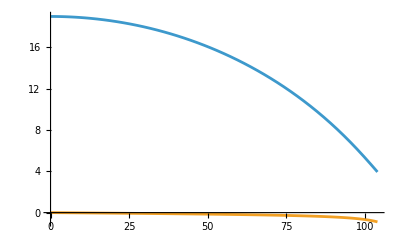

```mathematica
Plot[{rbarNum[t], urNum[t]}, {t, t0, tEnd}] (*rbarNum = blue, urNum = orange*)
```

Plot showing the in fall to the edge of the star

### Checking the analytic integral and NDSolve agree on the same τ(r̄)

```mathematica
tauNDSolve[tf_] := NIntegrate[α[rbarNum[t]]^2/E0, {t, t0, tf}]; (*Numerically solving one of the ODEs above for tau*)
```

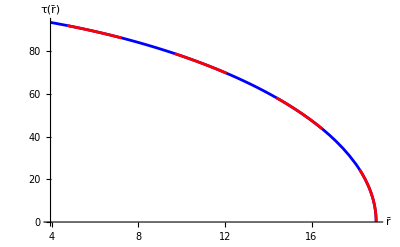

```mathematica
Show[Plot[tauIsotropic[rbar0, r], {r, rbar0, rbarStar}(*Plot from starting r0 down to R, as r decreases*), PlotStyle->Blue]
, ParametricPlot[{rbarNum[tf], tauNDSolve[tf]}, {tf, t0, tEnd},
PlotStyle->{Dashing[0.1], Red}], AxesLabel -> {"r̄", "τ(r̄)"}]
```

Proper times agree

## TOV ρ=constant solution.... Setting it up and checking limits

### Setting up Everything:

```mathematica
M = 1;
RStar = 5;
```

```mathematica
Mfunc[r_] = Piecewise[{{M r^3/RStar^3, r <= RStar}, {M, r>RStar}}];
grrTOV[r_] = (1 - (2Mfunc[r])/r)^-1; 
κ = √(2 M/RStar^3);
(*Integral constant I used by hand*)
Const = rBarSchw[RStar] √((1+√(1-(2M)/RStar))/(1-√(1-2 M/RStar))); (*Can use schw to convert RStar as the value should be the same inside and outside*)
rBarofrInside[r_]=Const √((1-√(1-2 Mfunc[r]/r))/(1+√(1-2 Mfunc[r]/r)));
rofRbarInside[R_]=1/κ √(1-Tanh[Log[R/Const]]^2);
```

#### Checking Inside and outside r̄ agree on RSTAR

```mathematica
rbarStar = rBarSchw[RStar];
RStarVal == N[rofRbarInside[%] /. M -> M /. RStar -> RStar] (*and it matches, % takes previous lines answer*)
```

RStarVal==5.

#### Checking limits of r and r̄ go to zero are actually zero in the star

Using the Limit function in Mathematica.....

```mathematica
0 == Limit[rBarofrInside[r], r->0]
0 == Limit[rofRbarInside[rbar], rbar -> 0]
```

True

True

Computing Limit by series expansion.....

```mathematica
0 == Limit[
	FullSimplify[
	Series[rBarofrInside[r], {r, 0, 1} (*Variable we are expanding "r", expand about "0", keep terms up to order "1"*)],
	0 < r < RStar
	],
	r->0
	]

0 == Limit[
	FullSimplify[
	Series[rofRbarInside[rbar], {rbar, 0, 1} (*Variable we are expanding "r", expand about "0", keep terms up to order "1"*)],
	rbar > 0 (*??*)
	],
	rbar->0
	]
```

True

True

#### Lapse and shift functions of the ρ=constant TOV metric:

```mathematica
αInside[rbar_]=(3/2 √(1-2 M/RStar)-1/2 √(1-2(M r^2)/RStar^3))/.r->rofRbarInside[rbar]; (*Lapse*)
AInside[rbar_]=rofRbarInside[rbar]/rbar;(*Shift*)
```

#### Checking if spacetime is regular at r̄ = 0 and it is

```mathematica
ALim0 = Limit[Simplify[Series[AInside[rbar], {rbar, 0, 1}], rbar >0], rbar->0] // N (*Means give it to me as a number*)
alphaLim0 = 
Limit[
Simplify[
Series[αInside[rbar], {rbar, 0, 1}], rbar >0],
rbar -> 0] // N
```

1.4315

0.661895

Plotting lapse and shift and honing in on the limits we computed above....

```mathematica
Show[Plot[AInside[rbar], {rbar, 0, 2}],
Plot[αInside[rbar], {rbar, 0, 2}, PlotStyle->Red],
Graphics[{Blue, Disk[{0,ALim0}, ImageScaled[{0.01, 0.02}]]}],
Graphics[{Red, Disk[{0, alphaLim0}, ImageScaled[{0.01, 0.02}]]}],
PlotRange -> All]
```

-Graphics-

## Solving ODEs of whole system for 1D radial drop with no external forces acting on the particle

Two coupled first order ODEs, solved using two initial conditions, which are as follows:
- We set the initial velocity of the particle to zero at t=0.
- We set the distance the particle drops from outside the star.
- Numerically integrate and solve these as done below.

### Constructing ODEs to be solved from paper

```mathematica
UtInside[rbar_,ur_]=1/αInside[rbar] √(1+ur^2/AInside[rbar]^2);
drBardtInside[rbar_, ur_] = 1/(AInside[rbar]^2 UtInside[rbar, ur])ur;
durdtInside[rbar_, ur_] = -αInside[rbar] UtInside[rbar, ur] Derivative[1][αInside][rbar] + ur^2/UtInside[rbar, ur]((Derivative[1][AInside][rbar])/AInside[rbar]^3);
```

### Numerically Integrating and Solving the 1st order system of coupled ODEs

Solver goes cuckoo at r = 0 unless I switch the sign of the velocity ur

```mathematica
t0 = 0;
tEnd = 2500;
rStop = 10^-4;

solIn = 
NDSolve[{rbar'[t] ==Piecewise[{{drBardt[rbar[t], ur[t]], rbar[t] >= rbarStar}, {drBardtInside[rbar[t], ur[t]], rbar[t] < rbarStar}}],
ur'[t] == Piecewise[{{durdt[rbar[t], ur[t]],rbar[t] >= rbarStar}, {durdtInside[rbar[t], ur[t]], rbar[t] < rbarStar}}], rbar[0] == rbar0, ur[0] == 0,
(*Center velocity switch*)
WhenEvent[ rbar[t] <= rStop, ur[t] -> -ur[t]]}, {rbar, ur}, {t, t0, tEnd}][[1]] (*Mathematica used to solving ODEs forward in time or from left to right, so impose at the ur = 0 turning point outside the star that the odes change accordingly and the sign flips to give it no ambiguity and to stop it from breaking*)
(*Inputted less stringent criteria on rbar in the WhenEvent (<=) function to allow the system to not breakdown and abandon ship when it didn't directly satisfy the strict equality I imposed*)

rbarNumIn = rbar /. solIn;
urNumIn = ur /. solIn;
```

{rbar→InterpolatingFunction[…],ur→InterpolatingFunction[…]}

```mathematica
tFinish = rbarNumIn["Domain"][[1,2]] (*Domain asks, "Over what time interval are you defined"*)

(*[[1, 2]] says take the first interval which is {tmin,tmax} and 2 extracts the max time from this.*)
```

2500.

```mathematica
tSurface=t/.FindRoot[rbarNumIn[t]==rbarStar,{t,100,10,500}(*{variable, initial guess, tmin, tmax}*)] (*t is just a variable here, this returns t ./ {t -> X seconds} ./ replaces all, so then t just becomes the number which becomes tSurface*)
```

104.013

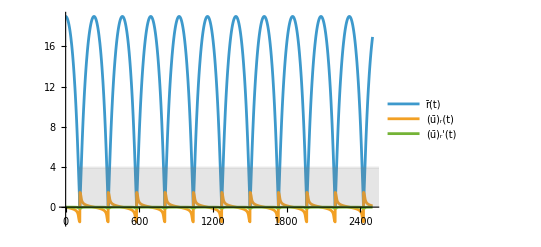

```mathematica
outFig=Show[Plot[{rbarNumIn[t],urNumIn[t],urNumIn'[t]},{t,t0,  tFinish},PlotLegends->LineLegend[Automatic,{"r̄(t)","(ū)_r(t)","(ū)_r'(t)"}]]
,Plot[rbarStar,{t,tSurface,tSurface+tFinish}, (*[const line, {Domain the line is drawn on}]*)PlotStyle->Directive[Gray,Opacity[0.1]],Filling->Bottom]](*Directive means... apply all of these stylings at the same time*)
```

All in line and even better than Sarp.

## Solving 1D drop with Hydrodynamic drag added into the problem

### Setting everything up.....

#### Setting up variables and equations to be used (no speed up factor)

```mathematica
m = 10^-6; (*mass of PBH?*)
Ivariable = 10; (*??? Just got from paper, something got to do with Coulomb something or other*) 
ρ = 10;
u[rbar_, ur_] = Abs[ur]/AInside[rbar];
P[rbar_] = ρ((√(1 - 2(M r^2)/RStar^3)-√(1 - 2 M/RStar))/(3 √(1 - 2 M/RStar) - √(1 - 2(M r^2)/RStar^3))) /.r->rofRbarInside[rbar];
(*Derived from TOV as I done last year*)

dpdtdragr[rbar_, ur_] = (-4π αInside[rbar](ρ + P[rbar])m^2(1 + 2 u[rbar, ur]^2)^2 Ivariable ur)/u[rbar, ur]^3;
```

#### New ODE with drag added

```mathematica
durdtInsideDrag[rbar_, ur_] = -αInside[rbar] UtInside[rbar, ur] Derivative[1][αInside][rbar] + ur^2/UtInside[rbar, ur]((Derivative[1][AInside][rbar])/AInside[rbar]^3) + 1/m(dpdtdragr[rbar, ur]);
```

#### Debugging the solver not working.... Was due to the very high speed up factor used, causing the velocity to be discontinuous and the solver not knowing what to do. Also didn’t work before I implemented machine precision as mentioned by Sarp.

Checking Limits to see why solver was not working, as mentioned was the speed up factor for the interior solution was not needed and only caused a discontinuity at the edge of the star where the two velocity equations had to match up. The solver was abandoning ship here. But, with limit analysis I fixed it.

```mathematica
FullSimplify[Limit[durdt[rbar, ur], {rbar->rbarStar, ur -> -.9}]] // N;
FullSimplify[Limit[durdtInside[rbar, ur], {rbar->rbarStar, ur -> -.9}]] // N;
```

```mathematica
FullSimplify[Limit[P[rbar], rbar -> rbarStar]];
FullSimplify[Limit[P[rbar], rbar -> 0]];
FullSimplify[Limit[AInside[rbar], rbar -> rbarStar]];
FullSimplify[Limit[αInside[rbar], rbar -> rbarStar]];
FullSimplify[Limit[dpdtdragr[rbar, ur], rbar -> rbarStar], ur ∈ Reals];
```

```mathematica
FullSimplify[Limit[durdtInsideDrag[rbar, ur], {rbar->rbarStar, ur -> -.9}]]  // N;
FullSimplify[Limit[durdt[rbar, ur], {rbar->rbarStar, ur -> -.9}]] // N;
-FullSimplify[Limit[durdtInsideDrag[rbar, ur], {rbar->rbarStar, ur -> -.9}]]+FullSimplify[Limit[durdt[rbar, ur], {rbar->rbarStar, ur -> -.9}]] // N;
FullSimplify[Limit[drBardt[rbar, ur], {rbar->rbarStar, ur -> -.9}]] // N;
FullSimplify[Limit[drBardtInside[rbar, ur], {rbar->rbarStar, ur -> -.9}]] // N;
FullSimplify[Limit[dpdtdragr[rbar, ur], {rbar->rbarStar, ur -> -.9}]] // N;
(*rbar(t) is fine, ur(t) is the problem, it is not continuous over the surface of the star*)
FullSimplify[Limit[durdt[rbar,ur],{rbar->rbarStar, ur -> -0.9}]-Limit[durdtInsideDrag[rbar,ur],{rbar->rbarStar, ur -> -0.9}]];
```

### Solving new ODEs with hydrodynamic drag

```mathematica
t0 = 0;
tEnd = 2500;
rStop = 10^-4;

solIn = 
NDSolve[{rbar'[t] ==Piecewise[{{drBardt[rbar[t], ur[t]], rbar[t] >= rbarStar}, {drBardtInside[rbar[t], ur[t]], rbar[t] < rbarStar}}],
ur'[t] == Piecewise[{{durdt[rbar[t], ur[t]],rbar[t] >= rbarStar}, {durdtInsideDrag[rbar[t], ur[t]], rbar[t] < rbarStar}}], rbar[0] == rbar0, ur[0] == 0, WhenEvent[rbar[t] <= rStop, ur[t] -> -ur[t]]}, {rbar, ur}, {t, t0, tEnd}, WorkingPrecision->40][[1]];

rbarNumIn = rbar /. solIn;
urNumIn = ur /. solIn;
```

NDSolve::ndsz: At t == 201.4208551146087493419450548604221137878, step size is effectively zero; singularity or stiff system suspected.

```mathematica
tFinish = rbarNumIn["Domain"][[1,2]];
tSurface=t/.FindRoot[rbarNumIn[t]==rbarStar,{t,80,10,tFinish}];
```

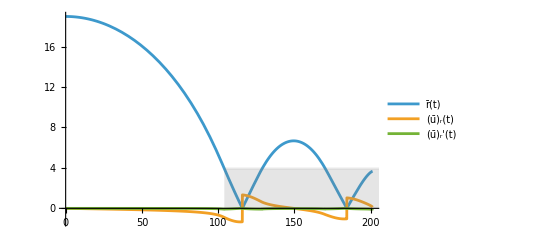

```mathematica
outFig=Show[Plot[{rbarNumIn[t],urNumIn[t],urNumIn'[t]},{t,t0, .999tFinish},PlotLegends->LineLegend[Automatic,{"r̄(t)","(ū)_r(t)","(ū)_r'(t)"}]]
,Plot[rbarStar,{t,tSurface,tSurface+tFinish}, (*[const line, {Domain the line is drawn on}]*)PlotStyle->Directive[Gray,Opacity[0.1]],Filling->Bottom]](*Directive means... apply all of these stylings at the same time*)
```

Solver does not work when inside the star at the point seen in the graph above, as the unavoidable singularity in the drag equation blows up here when ur goes to 0 inside.

## Going to 2D adding ϕ component

## Setting up new 2D ODEs with drag of course...

### Setting up ODEs

#### Outside Star

```mathematica
Ut[rbar_, ur_, uphi_] = (√(1 + (ur/A[rbar])^2 + (uphi/(rbar A[rbar]))^2))/α[rbar];

drBardt[rbar_, ur_, uphi_] = 1/(A[rbar]^2 Ut[rbar, ur, uphi])ur;

dphidtOutside[rbar_,ur_, uphi_] = 1/(rbar^2*A[rbar]^2*Ut[rbar, ur,uphi])uphi;

durdt2DOutside[rbar_, ur_, uphi_] = -α[rbar] Ut[rbar, ur, uphi] Derivative[1][α][rbar] + ur^2/Ut[rbar, ur, uphi]((Derivative[1][A][rbar])/A[rbar]^3) + uphi^2/Ut[rbar, ur, uphi](1/(rbar^3 *A[rbar]^2) + (Derivative[1][A][rbar])/(rbar^2*A[rbar]^3));
```

#### Inside Star

```mathematica
UtInside[rbar_, ur_, uphi_] = (√(1 + (ur/AInside[rbar])^2 + (uphi/(rbar AInside[rbar]))^2))/αInside[rbar];
ϵ = 10^-1; (*regularisation parameter*)
ρ = 10;
umagphi[rbar_, ur_, uphi_] = (√(ur^2+(uphi/rbar)^2 + ϵ^2))/AInside[rbar];(*paper eqn ut and umagphi*)

drBardtInside[rbar_, ur_, uphi_] = 1/(AInside[rbar]^2 UtInside[rbar, ur, uphi])ur;

dphidtInside[rbar_, ur_, uphi_] = 1/(rbar^2 AInside[rbar]^2 UtInside[rbar, ur, uphi])uphi;

dpdtdragphi[rbar_, ur_, uphi_] = 1/umagphi[rbar, ur, uphi]^3(-4π αInside[rbar]*(ρ + P[rbar])*m^2*(1 + 2 umagphi[rbar, ur, uphi]^2)^2 *Ivariable *uphi);

duphidtInside[rbar_, ur_, uphi_] = η/m(dpdtdragphi[rbar, ur, uphi]);

dpdtdragr[rbar_, ur_, uphi_] = (-4π αInside[rbar](ρ + P[rbar])m^2(1 + 2 umagphi[rbar, ur, uphi]^2)^2 Ivariable ur)/umagphi[rbar, ur, uphi]^3;

durdt2DInside[rbar_, ur_, uphi_] = -αInside[rbar] UtInside[rbar, ur, uphi] Derivative[1][αInside][rbar] + ur^2/UtInside[rbar, ur, uphi]((Derivative[1][AInside][rbar])/AInside[rbar]^3) + uphi^2/UtInside[rbar, ur, uphi](1/(rbar^3 AInside[rbar]^2) + (Derivative[1][AInside][rbar])/(rbar^2 AInside[rbar]^3)) +  η/m(dpdtdragr[rbar, ur, uphi]);
```

#### Defining Initial Conditions

```mathematica
EnergyPerUnitMass[ptilde_, eccen_] := √(((ptilde -2)^2 - 4 eccen^2)/(ptilde(ptilde - 3 - eccen^2)));
LPerUnitMass[ptilde_, M_, eccen_] := (ptilde M)/(√(ptilde - 3 - eccen^2));
ptildefunc[p_, Mass_] := p/Mass;
rapoapsis[eccen_, ptilde_, Mass_] := ((ptilde) Mass)/(1 - eccen)
rperiapsis[eccen_, ptilde_] := ptilde/(1+eccen)
```

```mathematica
M=1;
eccentricity = 0.4;
semilatrecP = 6;
ptilde = ptildefunc[semilatrecP, M];

Energy = EnergyPerUnitMass[ptilde, eccentricity];
AngularMomentumUphi0 = LPerUnitMass[ptilde, M, eccentricity];
r0 = rapoapsis[eccentricity, ptilde, M];
rbar0 = rBarSchw[r0];
```

#### Must satisfy this inequality

```mathematica
ptilde
5(1+eccentricity)
ptilde < 5(1+eccentricity)
```

6

7.

True

#### Solving the ODEs

```mathematica
t0=0;
tEnd=10000;

η=1; (*Speed up parameter*)

solIn=NDSolve[
{
rbar'[t]==
Piecewise[
{
{drBardt[rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{drBardtInside[rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
ur'[t]==
Piecewise[
{
{durdt2DOutside[rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{durdt2DInside[rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
uphi'[t]==
Piecewise[
{
{0,rbar[t]>=rbarStar},
{duphidtInside[rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
phi'[t]==
Piecewise[
{
{dphidtOutside[rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{dphidtInside[rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
rbar[0]== rbar0,
ur[0]==0,
phi[0]==0,
uphi[0]==AngularMomentumUphi0 
},
{rbar,ur,phi,uphi},
{t,t0,tEnd},
WorkingPrecision->40,
MaxSteps->20000
][[1]];
```

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (40.).

umag causing problems as velocities go to zero.

```mathematica
rbarNumIn = rbar /. solIn;
urNumIn = ur /. solIn;
phiNumIn = phi /. solIn;
uphiNumIn = uphi /. solIn;
```

```mathematica
tFinish = rbarNumIn["Domain"][[1,2]]
tSurface=t/.FindRoot[rbarNumIn[t]==rbarStar,{t,10,10,tFinish}]
```

10000.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal, but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

153.272

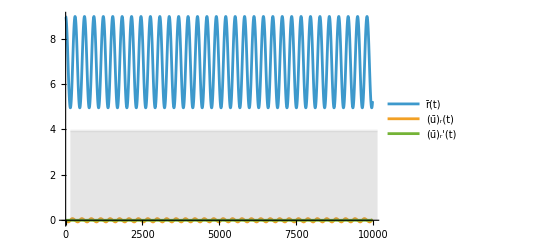

```mathematica
outFigRadial=Show[Plot[{rbarNumIn[t],urNumIn[t],urNumIn'[t]},{t,t0,.999 tFinish},PlotLegends->LineLegend[Automatic,{"r̄(t)","(ū)_r(t)","(ū)_r'(t)"}]],Plot[rbarStar,{t,tSurface,tSurface+tFinish},PlotStyle->Directive[Gray,Opacity[0.1]],Filling->Bottom]]
```

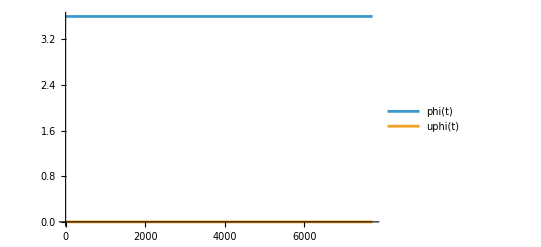

```mathematica
outFigAngular=Plot[{uphiNumIn[t],uphiNumIn'[t]},{t,t0,.999 tFinish},PlotLegends->LineLegend[Automatic,{"phi(t)","uphi(t)","uphi'(t)"}]]
```

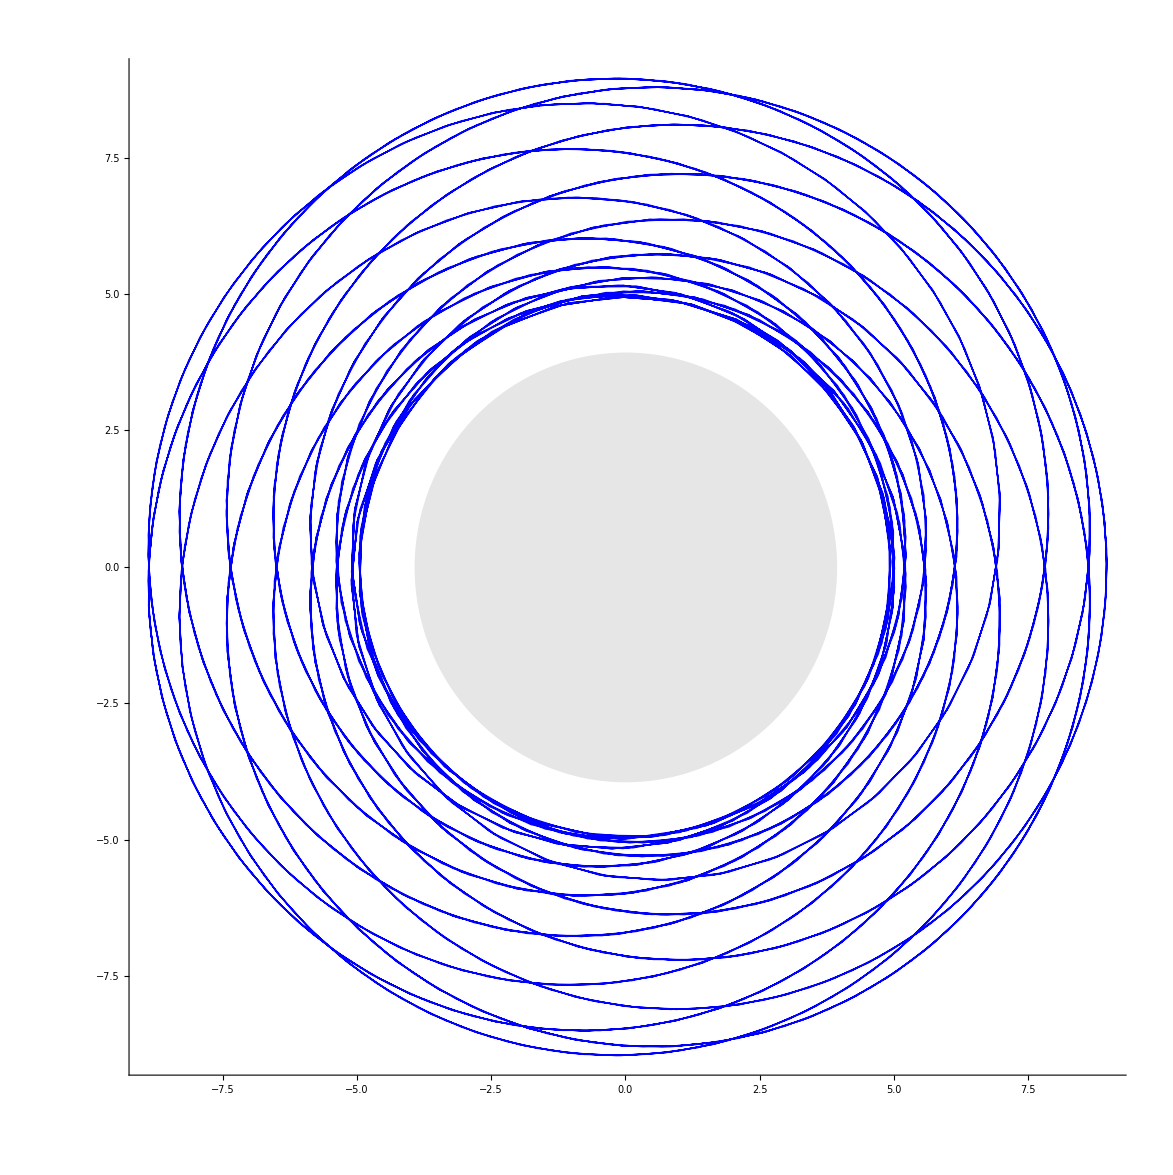

```mathematica
x[t_]:=rbarNumIn[t] Cos[phiNumIn[t]];
y[t_]:=rbarNumIn[t] Sin[phiNumIn[t]];
orbit2D=ParametricPlot[{x[t],y[t]},{t,t0,0.999 tFinish},AspectRatio->Automatic,AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Thick,Blue}];
(*Automatic scale makes the aces the same scale*)
centralBody=Graphics[{GrayLevel[0.9],Disk[{0,0},rbarStar]}];
Show[centralBody, orbit2D,AspectRatio->Automatic,PlotRange->All, Axes -> True]
```

eccentric orbit and dig thru literature for u cubed and input speed factor.

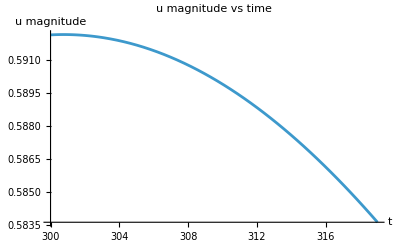

```mathematica
Plot[Evaluate[umagphi[rbarNumIn[t],urNumIn[t],uphiNumIn[t]]/. solIn],{t,300,319},PlotRange->All,AxesLabel->{"t","u magnitude"},PlotLabel->"u magnitude vs time"]
```

```mathematica
rbarNumIn[160]
```

8.93692478443256367052797549403772269868

#### Converting back to the areal radius to see the graphs and if it is different

```mathematica
(*Areal radius as a function of isotropic radius*)rFromRbar[rbar_]:=Piecewise[{{A[rbar]*rbar,rbar>=rbarStar},(*exterior*){AInside[rbar]*rbar,rbar<rbarStar}    (*interior*)}];

(*Areal radius along the orbit*)
arealr[t_]:=rFromRbar[rbarNumIn[t]];
```

```mathematica
x[t_]:=arealr[t] Cos[phiNumIn[t]];
y[t_]:=arealr[t] Sin[phiNumIn[t]];
```

```mathematica
orbit2D=ParametricPlot[{x[t],y[t]},{t,t0,0.999 tFinish},AspectRatio->1,AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Thick,Blue}];
```

```mathematica
(*Areal radius of the stellar surface*)
rstarAreal=A[rbarStar] rbarStar;

centralBody=Graphics[{GrayLevel[0.9],Disk[{0,0},rstarAreal]}];
```

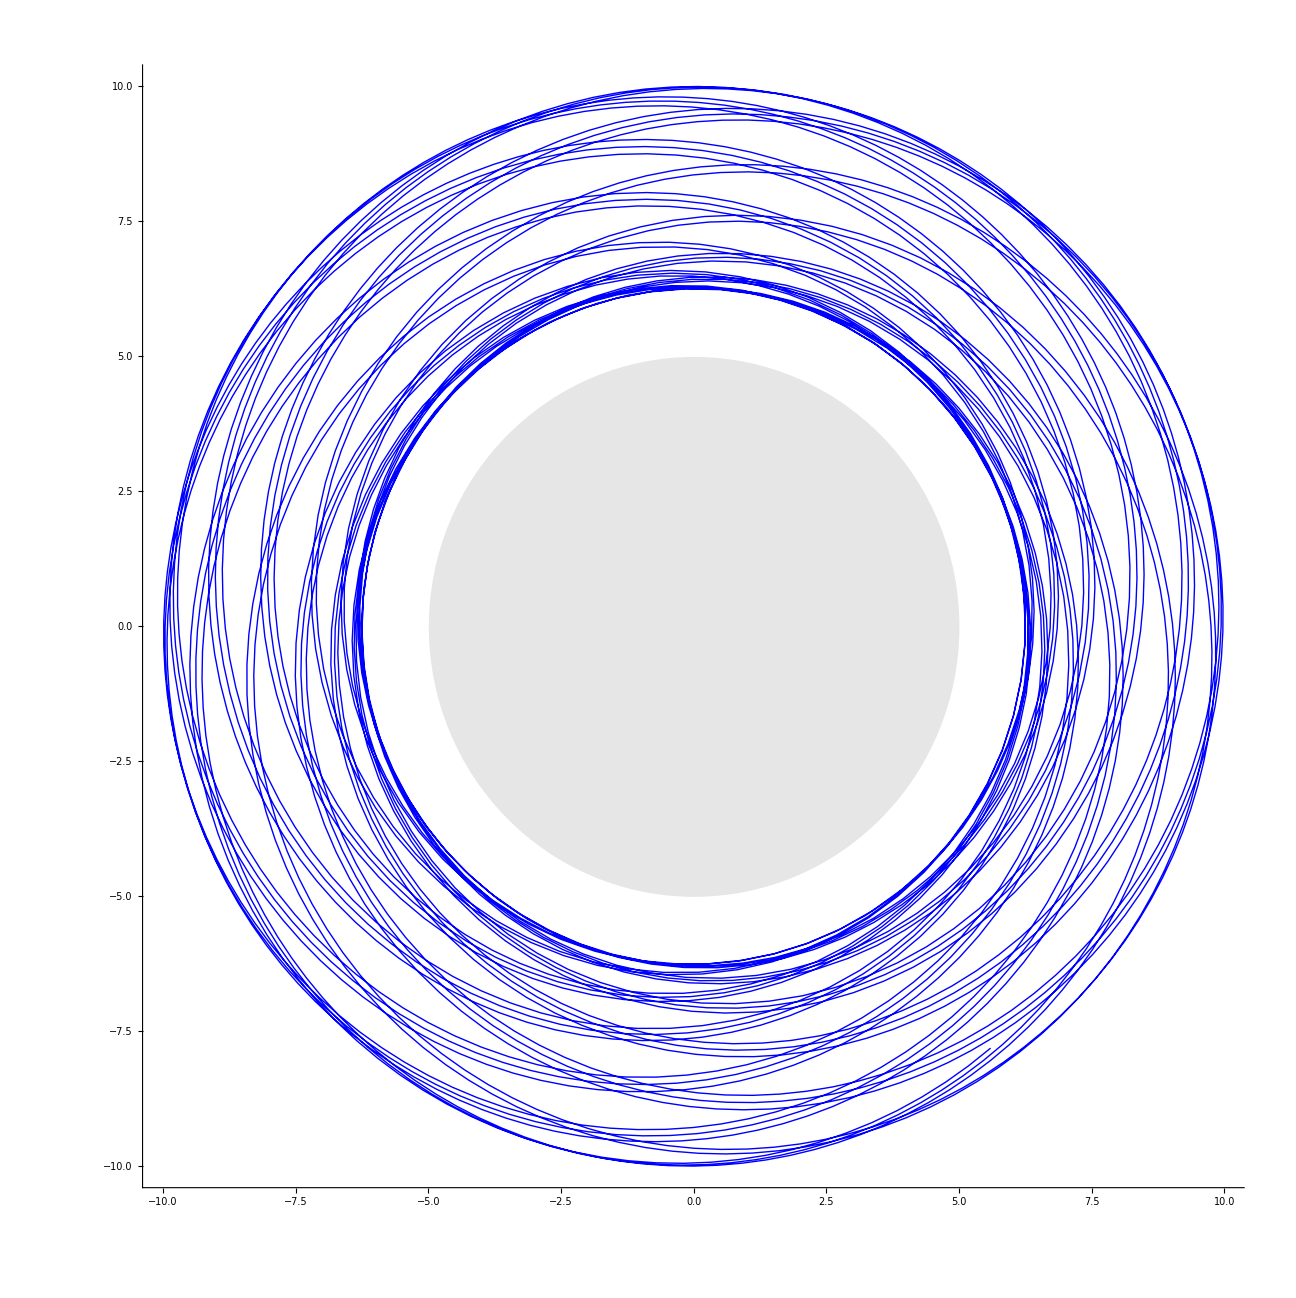

```mathematica
Show[centralBody, orbit2D,AspectRatio->Automatic,PlotRange->All, Axes -> True]
```

Initially though that it was stopping because the velocities were zero and that it was at the centre, which turned out to be naive, checked the value or rbarNumIn and this showed that it was not at zero, and it is the u^3 term once again causing this artificial, fictitious behaviour as a result of the coordinate choices I assume.
In reflection, it cannot be a singularity here and it a result of numerical stiffness build up in the integration

### Capturing the PBH from infinity

Assuming PBH comes from infinity and just hits in and enters the star

#### Approaching the problem differently, using Keplerian orbits on the outside of the star and then GR on the inside to reduce the stiffness of the problem causing the error in the solver.

Setting v_inf to something physical is essential, most dark matter comes from the galactic halo, where things move at roughly 200km/s so with setting c = 1, vinf should be 10^-3 which implies the Energy at infinity should be approximately equal to 1 and very little energy loss is needed to bound the orbit.

#### Defining Initial Data Functions

```mathematica
vinf = 10^-3;
```

```mathematica
InitialEnergyAtInfinity[vinf_] := 1/(√(1 - vinf^2)); (*eq47 2404 paper*)
```

```mathematica
(*general formula for the magnitude of the velocity, for a general spherically symmetric Isotropic metric*)
umagVel[ur_, uphi_, rbar_] := √(ur^2 + (uphi/rbar)^2)
umagE[Energy_, rbar_] := A[rbar] √((Energy/α[rbar])^2 - 1); (*eq 48 in paper*)
```

```mathematica
(*Defining the Impact angle, which is the angle between the radial vector and the PBH's velocity vector*) (*It is the angle the PBH enters the star*)

urInit[psi_, Einit_] := -umagE[Einit , rbarStar]Cos[psi];
uphiInit[psi_, rbarStar_, Einit_] := rbarStar umagE[Einit ]Sin[psi]; (*Is defining angular momentum, L is equal to this*)
```

#### Setting the Initial conditions

```mathematica
(*we start at rbarStar*)
phi0 = 0;
Einf = InitialEnergyAtInfinity[vinf];
 u = umagE[Einf, rbarStar];
ImpactAngle = Pi/4; (*In radians, measured from center of star to the position of particle, in unit circle fashion, pi/2 corresponds to grazing the star as it enters and 0 corresponds to a radial drop*)
ur0 = -u*Cos[ImpactAngle];
uphi0 = (rbarStar)(u) Sin[ImpactAngle];
```

#### Sanity Check to see if the two energy formulas match up

```mathematica
Einf = InitialEnergyAtInfinity[vinf] //N
α[rbarStar]^2  Ut[rbarStar, ur0, uphi0] //N (*This Ut was upper indexed*)
```

1.

1.

#### Performing the inside integration

```mathematica
t0=0;
tEnd=10000;

solIn=NDSolve[
{
rbar'[t]==
If[
rbar[t] >=rbarStar,
drBardt[rbar[t],ur[t],uphi[t]],
drBardtInside[rbar[t],ur[t],uphi[t]]
],
ur'[t]==
If[
rbar[t] >=rbarStar,
durdt2DOutside[rbar[t],ur[t],uphi[t]],durdt2DInside[rbar[t],ur[t],uphi[t]]
],
uphi'[t]==
If[
rbar[t] >= rbarStar,
0,
duphidtInside[rbar[t],ur[t],uphi[t]]
],
phi'[t]==
If[
rbar[t] >= rbarStar,
dphidtOutside[rbar[t],ur[t],uphi[t]],dphidtInside[rbar[t],ur[t],uphi[t]]
],
rbar[0]==rbarStar,
ur[0]==ur0,
uphi[0]==uphi0,
phi[0]==phi0,

WhenEvent[
rbar[t] - rbarStar >0 && ur[t] >0,
"StopIntegration"
] (*Stop Integration if the PBH exits the star again*)
},
{rbar,ur,uphi,phi},{t,t0,tEnd},

WorkingPrecision->40,
MaxSteps->20000, 
Method->{"StiffnessSwitching"}
][[1]];
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 1/2 (-4-√15)+1/2 (4+√15).

Round::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating Round[Sign[1/2 (-4-√15)+1/2 (4+√15)]].

NDSolve::ndinid: Initial condition Sign[1/2 (-4-√15)+1/2 (4+√15)] is not in the range specified by the discrete variable NDSolve`s$453821.

Notes for next meeting

- Went through papers using ctrl F and also put them through, couldnt see anything to help with 1/u^3
- added in the epsilon to fix the issue, worked and got to the centre, although abruptly, maybe I can just turn off the drag if it becomes less important or something
- looked at PBH coming from infinity and got that setup as in paper, although issue with singularity persisted
- made orbits eccentric and based off of orbital parameters ptilde and eccentricity and now it wont work in terms of going inside the star, not sure why?